```mathematica
parse="EvenQ[dd]]";
SyntaxLength[parse]
StringTake[parse,%]
```

9

EvenQ[dd]

```mathematica
ClearAll[a,x,fList,func,degree,center,evalString];
a=RandomInteger[{1,4}];
fList=RandomChoice[{
{Exp[a x^2],{3,4,5,6},{0,1,-1,2,-2}},
{Log[a x+1],{3,4,5,6},{0,1,2}}
}
];
func=fList[[1]];
degree=RandomChoice[fList[[2]]];
center=RandomChoice[fList[[3]]];
evalString="ClearAll[a,x,func,degree,center];a="<>ToString[a]<>";func="<>ToString[InputForm[func]]<>";degree="<>ToString[degree]<>";center="<>ToString[center]<>";";
```

```mathematica
$SyntaxHandler=Function[{string,position},
Print[string];
Print[position];
Return[$Failed];
]
```

Function[{string,position},Print[string];Print[position];Return[$Failed];]

```mathematica
$SyntaxHandler["123",50]
```

123

50

Return[$Failed]

```mathematica
TeXForm[Exp[3x]]
```

e^{3 x}

```mathematica
SyntaxQ["Sind[x]"]
```

True

```mathematica
ToExpression["e^(0)",TraditionalForm]
```

1

```mathematica
InputForm[Normal[Series[Log[3x+1],{x,2,6}]]]
```

(3*(-2 + x))/7 - (9*(-2 + x)^2)/98 + (9*(-2 + x)^3)/343 - (81*(-2 + x)^4)/9604 + (243*(-2 + x)^5)/84035 - (243*(-2 + x)^6)/235298 + Log[7]

```mathematica
Apply
```

```mathematica
Catch[
If[Not[SyntaxQ[#]],Throw["Syntax Error"]];
If[SameQ[Simplify[Normal[Series[func,{x,center,degree}]]-ToExpression[#]],0],Throw["Correct"],Throw["Incorrect"]]
]&@@{}
```

```mathematica
ClearAll[A,u,v,rank];
Block[{a,n,n1,n2},
rank= RandomInteger[]+1;
u=0;
v=RandomSample[{-5,-4,-3,-2,-1,0,1,2,3,4,5,1/2,1/3,1/4,1/5,-1/2,-1/3,-1/4,-1/5},3];Print[v];
If[rank==1,
u=RandomSample[{-5,-4,-3,-2,-1,1,2,3,4,5,1/2,1/3,1/4,1/5,-1/2,-1/3,-1/4,-1/5},3];Print[u];
n=Cross[v,u];
A=Table[n a,{a,RandomChoice[{-5,-4,-3,-2,-1,1,2,3,4,5,1/2,1/3,1/4,1/5,-1/2,-1/3,-1/4,-1/5},3]}];
,
{n1,n2}=NullSpace[{v}];
A=Table[n1 a[[1]]+n2 a[[2]],{a,RandomChoice[{-5,-4,-3,-2,-1,1,2,3,4,5,1/2,1/3,1/4,1/5,-1/2,-1/3,-1/4,-1/5},{3,2}]}];
];];
evalString="ClearAll[A,u,v,rank];A="<>ToString[InputForm[A]]<>";u="<>ToString[InputForm[u]]<>";v="<>ToString[InputForm[v]]<>";rank="<>ToString[InputForm[rank]]<>";"
MatrixForm[A]
TeXForm[MatrixForm[A]]
```

{-2,-5,-1/2}

{-3,-1/2,-1/4}

ClearAll[A,u,v,rank];A={{-1, -1, 14}, {-1/4, -1/4, 7/2}, {-2, -2, 28}};u={-3, -1/2, -1/4};v={-2, -5, -1/2};rank=1;

(-1 | -1 | 14
-1/4 | -1/4 | 7/2
-2 | -2 | 28)

\left(
\begin{array}{ccc}
 -1 & -1 & 14 \\
 -\frac{1}{4} & -\frac{1}{4} & \frac{7}{2} \\
 -2 & -2 & 28 \\
\end{array}
\right)

```mathematica
u=RandomSample[{-5,-4,-3,-2,-1,1,2,3,4,5,1/2,1/3,1/4,1/5,-1/2,-1/3,-1/4,-1/5},3];
n=Cross[v,u];
A=Table[n a,{a,RandomChoice[{-5,-4,-3,-2,-1,1,2,3,4,5,1/2,1/3,1/4,1/5,-1/2,-1/3,-1/4,-1/5},3]}]
```

{{-7/2,-9/2,-15/8},{7/12,3/4,5/16},{35/6,15/2,25/8}}

```mathematica
Table[-1/i,{i,5}]
```

{-1,-1/2,-1/3,-1/4,-1/5}

```mathematica
{n1,n2}=NullSpace[{{1,2,3}}]
n1
n2
```

{{-3,0,1},{-2,1,0}}

{-3,0,1}

{-2,1,0}

```mathematica
Table[n1 a[[1]]+n2 a[[2]],{a,RandomChoice[{-5,-4,-3,-2,-1,1,2,3,4,5,1/2,1/3,1/4,1/5,-1/2,-1/3,-1/4,-1/5},{3,2}]}]//MatrixForm
```

(5 | 5 | -5
11/2 | 1/4 | -2
11/2 | -2 | -1/2)

```mathematica
Function[rank,
Catch[
Module[{inRank},
inRank=ToExpression[rank];
If[Not[IntegerQ[inRank]],Throw["Rank must be an integer."]];
If[inRank<0,Throw["Rank must be a non-negative integer."]];
If[PossibleZeroQ[-inRank],Throw["&#10003;"],Throw["&#10007;"]]
]
]
]@@{"1"}
```

&#10007;

```mathematica
Function[{total,vectors},
Catch[
Throw[##]
]
]@@{"1","2","3"}
```

2

```mathematica
(Catch[
Scan[If[Not[SyntaxQ[#]],Throw["Syntax error is found in "<>#]]&,{##2}];
If[3-#1≠rank,Throw["You have provided an incorrect number of solutions (either too many, or too few)"]];
Module[{exprList,i},
exprList=Map[ToExpression,{##2}];
For[i=1,i<=#1,i++,
If[Not[VectorQ[exprList[[i]],NumericQ]],Throw["Answer ("<>ToString[i]<>") is not a valid vector"]];
If[Length[exprList[[i]]]≠3,Throw["Answer ("<>ToString[i]<>") is not a three-dimensional vector"]];
If[Norm[exprList[[i]]]<10^(-6),Throw["Your answer ("<>ToString[i]<>") seems to be a zero vector"]]
];
If[rank==1,
If[MatrixRank[exprList,Tolerance->10^(-6)]<2,Throw["You must provide linearly independent vectors"]];
If[Norm[A.exprList[[1]]]>10^(-6),Throw["Your answer (1) does not seem to be a solution"]];
If[Norm[A.exprList[[2]]]>10^(-6),Throw["Your answer (2) does not seem to be a solution"]];
Throw["&#10003;"];
,
If[Norm[A.exprList[[1]]]>10^(-6),Throw["Your answer (1) does not seem to be a solution"]];
Throw["&#10003;"];
]
];
])&@@{2,"{2,5,1/2}","{3,1/2,1/4}"}
```

&#10003;

```mathematica
ToString
```

```mathematica
MatrixRank[{u,v,{0,0,0}}]
```

2

```mathematica
PossibleZeroQ[{0,0}]
```

{True,True}

```mathematica
A.u
```

{0,0,0}

1/2 (-6+7 x-x^2)

-7+(17 x)/2-(3 x^2)/2

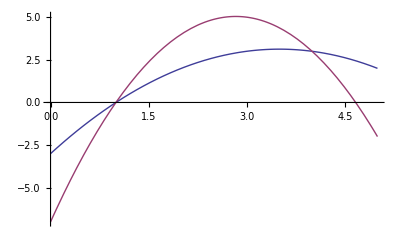

```mathematica
{a,b,c}={1,2,4};
{fa,fb,gb,fc}={0,2,4,3};
f[x_]:=fa (x-b)/(a-b)(x-c)/(a-c)+fb (x-a)/(b-a)(x-c)/(b-c)+fc (x-b)/(c-b)(x-a)/(c-a);
g[x_]:=fa (x-b)/(a-b)(x-c)/(a-c)+gb (x-a)/(b-a)(x-c)/(b-c)+fc (x-b)/(c-b)(x-a)/(c-a);
Print[Simplify[f[x]]];
Print[Simplify[g[x]]];
Plot[{f[x],g[x]},{x,a-1,c+1}]
```

```mathematica
density = RandomChoice[{1/2,1/3,1/4,1/5,1,2,3,4,5}];
```

```mathematica
ClearAll[x,y,f,g,if,ig,a,b,c,fa,fb,graph,graphString,density]
Block[{},
c=RandomChoice[{1/2,1/3,1/4,1,2,3,4}];
a=RandomChoice[{1/5,1/4,1/3,1/2,1}];
b=RandomChoice[{2,3,4}];
density = RandomChoice[{1/2,1/3,1/4,1/5,1,2,3,4,5}];
f=(c #^2)&;
fa=f[a];fb=f[b];
g = Simplify[fa(#-b)/(a-b)+fb(#-a)/(b-a)]&;
graph =Show[{
Plot[{f[x],g[x]},{x,a-1,b+1},PlotStyle->None,Filling->{1->{2}},
PlotRange->{{a,b},{fa,fb}}],
Plot[{f[x],g[x]},{x,a-1,b+1},PlotStyle->{Directive[Thick,Purple],Directive[Thick,Red]},
PlotRange->{{Min[a-1,-1/2],b+1},{Min[fa-1,-1/2],fb+1}}]
},
Axes->True;
AspectRatio->1;
AxesStyle->Directive[FontSize->16,Thickness[0.003]],
AxesOrigin->{-0.01,-0.01},
PlotRange->{{Min[a-1,-1/2],b+1},{Min[fa-1,-1/2],fb+1}},
AxesLabel->{Style[TraditionalForm[x],FontSize->20],Style[TraditionalForm[y],FontSize->20]}
];
graphString =StringReplace[ExportString[graph,"SVG"],"<!DOCTYPE svg PUBLIC \"-//W3C//DTD SVG 1.1//EN\" \"http://www.w3.org/Graphics/SVG/1.1/DTD/svg11.dtd\">\n"->""] ;
if=Sqrt[#/c]&;
ig = Simplify[a(#-fb)/(fa-fb)+b(#-fa)/(fb-fa)]&;
]
```

```mathematica
(Catch[
Scan[If[Not[SyntaxQ[#]],Throw["Syntax error is found in \""<>#<>"\""]]&,{##2}];
Module[{upperLimit,lowerLimit,func,iVar,strippedIVar,transformedFunc},
strippedIVar=StringReplace[#5,Whitespace->""];
If[Or[StringLength[strippedIVar]>1,StringLength[strippedIVar]<1,Not[LetterQ[strippedIVar]]],Throw["Integration variable must be a single letter"]];
transformedFunc=StringReplace[#4,{strippedIVar~~Whitespace~~"("->strippedIVar<>"*(",strippedIVar<>"("->strippedIVar<>"*("}];
Block[{x},
{upperLimit,lowerLimit,func,iVar}=Map[ToExpression[#,TraditionalForm]&,{#2,#3,transformedFunc,strippedIVar}];
Print[{upperLimit,lowerLimit,func,iVar}];
func=ReplaceAll[func,iVar->x];
If[Or[Not[NumericQ[upperLimit]],Not[NumericQ[lowerLimit]]],Throw["Limits of integration must be real numbers"]];
If[PossibleZeroQ[Simplify[ density (g[x]^2 - f[x]^2)/2 - func]],
If[And[PossibleZeroQ[upperLimit - b],PossibleZeroQ[lowerLimit - a]],
Throw["&#10003;"],
Throw["Your limits of integration are not correct"]
]
,
If[PossibleZeroQ[Simplify[ density x (if[x] - ig[x]) - func]],
If[And[PossibleZeroQ[upperLimit - fb],PossibleZeroQ[lowerLimit -fa]],
Throw["&#10003;"],
Throw["Your limits of integration are not correct"]
]
,
Throw["The integrand is not correct"]
]
]
];
];
])&@@{4,"32","2","x((x/2)^(1/2) - (8+x)/10)/5","x"}
```

{32,2,1/5 (1/10 (-8-x)+(√x)/(√2)) x,x}

&#10003;

```mathematica
Catch[If[Not[SyntaxQ[#2]],Throw[\"Syntax Error\"]];If[PossibleZeroQ[Simplify[" + kTalker.executeCommand("InputForm[Normal[Series[func,{x,center,degree}]]]") + "-ToExpression[#2]]],Throw[\"&#10003;\"],Throw[\"&#10007;\"]]]
```

```mathematica
{a,b,fa,fb,f[x],g[x],if[x],ig[x],density}
```

{1,4,2,32,2 x^2,-8+10 x,(√x)/(√2),(8+x)/10,1/5}

```mathematica
A={{1,2},{3,4}}
```

{{1,2},{3,4}}

```mathematica
Inverse[A]
```

{{-2,1},{3/2,-1/2}}

```mathematica
A^(-1)
```

{{1,1/2},{1/3,1/4}}

```mathematica
Block[{n,k,flist,iflist,x},
n=5;
flist = Table[x Log[x]^k,{k,1,n}];
iflist = Map[Integrate[#,x]&,flist];
Grid[
Transpose[
{flist,iflist}
],
Frame->All
]
]
```

x Log[x] | -x^2/4+1/2 x^2 Log[x]
x Log[x]^2 | x^2/4-1/2 x^2 Log[x]+1/2 x^2 Log[x]^2
x Log[x]^3 | -(3 x^2)/8+3/4 x^2 Log[x]-3/4 x^2 Log[x]^2+1/2 x^2 Log[x]^3
x Log[x]^4 | (3 x^2)/4-3/2 x^2 Log[x]+3/2 x^2 Log[x]^2-x^2 Log[x]^3+1/2 x^2 Log[x]^4
x Log[x]^5 | -(15 x^2)/8+15/4 x^2 Log[x]-15/4 x^2 Log[x]^2+5/2 x^2 Log[x]^3-5/4 x^2 Log[x]^4+1/2 x^2 Log[x]^5

a/c==l/a==h/b     and      b/c==h/a==r/b      and       h/l==r/h==a/b

```mathematica
ClearAll[a,b,c]
```